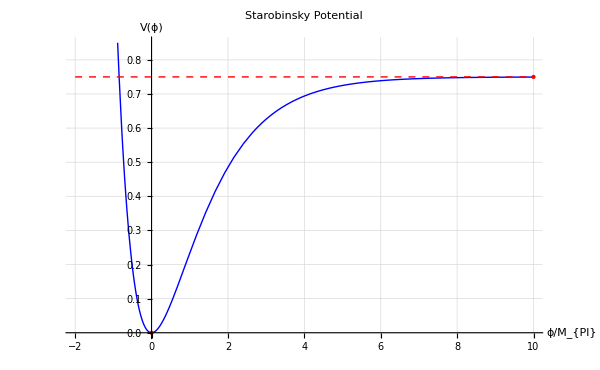

```mathematica
V[phi_]:=(3 MPl^2 M^2)/4 (1-Exp[-Sqrt[2/3] phi/MPl])^2
MPl=1;
M=1;
Plot[V[phi],{phi,-2,10},PlotStyle->{Thick,Blue},AxesLabel->{"ϕ/M_{Pl}","V(ϕ)"},PlotLabel->"Starobinsky Potential",GridLines->Automatic,ImageSize->600,PlotRange->{0,0.85},Epilog->{{Dashed,Red,Line[{{-2,3/4},{10,3/4}}]},{Red,PointSize[Large],Point[{0,0}]},{Red,PointSize[Large],Point[{10,3/4}]}}]
```